## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

```mathematica
removeInputFiles = True;
removeOutputFiles = True;

rxnName="PGMd";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;

(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;

(*Fit mode. 1 = base data fit, 2 = data sampled randomly within uncertainty uncertainty bound, 3 = data sampled via parameter sweep in range*)
(*Note: Mode 3 requires additional customization in the related section based on what data is being fit*)
nSamplesUncertainty=10;
modeFit = 1;

(* user will need to change this path *)
pathMASSef = "C:/MASSef/";
directoryMASSpyExport = "C:/MASSef/examples/Manuscript_Fitting/" 
kineticDataFileName =  "kinetic_data_manuscript_basic.csv";

mainFolder = "fit_PGMd_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

C:/MASSef/examples/Manuscript_Fitting/

Working dir:C:\MASSef\examples\Manuscript_Fitting\

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

((3pg)^c⇌(2pg)^c)^PGMd

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 0.189 | 0.17955
0.19845 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | 0.0002 | 0.000173
0.000227 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | 0.00019 | 0.000155
0.000225 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null
23dpg | 0.0001 | 626.718 | 605.827
647.608 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | Null
23dpg | 0.0001 | 417.812 | 393.123
442.501 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((3pg)^c⇌(2pg)^c)^PGMd

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 0.189 | 0.17955
0.19845 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | 0.0002 | 0.000173
0.000227 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | 0.00019 | 0.000155
0.000225 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null
23dpg | 0.0001 | 626.718 | 605.827
647.608 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | Null
23dpg | 0.0001 | 417.812 | 393.123
442.501 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_PGMd[c] + 23dpg[c] <=> E_PGMd[c]&23dpg",
				"E_PGMd[c]&23dpg + 3pg[c] <=> E_PGMd[c]&23dpg&3pg",
				"E_PGMd[c]&23dpg&3pg <=> E_PGMd[c]&23dpg&2pg",
				"E_PGMd[c]&23dpg&2pg <=> E_PGMd[c]&23dpg + 2pg[c]"};

enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((PGMd^c)_^+(23dpg)^c⇌(PGMd^c&(23dpg)^c)_^)^PGMd1,((PGMd^c&(23dpg)^c)_^+(3pg)^c⇌(PGMd^c&(23dpg)^c&(3pg)^c)_^)^PGMd2,((PGMd^c&(23dpg)^c&(2pg)^c)_^⇌(PGMd^c&(23dpg)^c)_^+(2pg)^c)^PGMd3,((PGMd^c&(23dpg)^c&(3pg)^c)_^⇌(PGMd^c&(23dpg)^c&(2pg)^c)_^)^PGMd4}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PGMd^c&(23dpg)^c)_^+(3pg)^c⇌(PGMd^c&(23dpg)^c&(3pg)^c)_^)^PGMd2,Overscript[(PGMd^c&(23dpg)^c&(2pg)^c)_^⇌(PGMd^c&(23dpg)^c)_^+(2pg)^c, PGMd3],((PGMd^c&(23dpg)^c&(3pg)^c)_^⇌(PGMd^c&(23dpg)^c&(2pg)^c)_^)^PGMd4};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, {},{}, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((PGMd^c&(23dpg)^c&(3pg)^c)_^-((PGMd^c&(23dpg)^c&(2pg)^c)_^)/K_PGMd4) Volume_c k_PGMd4^⟶}

Volume_c (-(PGMd^c&(23dpg)^c&(2pg)^c)_^ k_PGMd4^⟵+(PGMd^c&(23dpg)^c&(3pg)^c)_^ k_PGMd4^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

### In vivo flux data (if desired)

```mathematica
haldaneRatiosList[[1]]
metsFull
```

(k_PGMd2^⟶ k_PGMd3^⟶ k_PGMd4^⟶)/(k_PGMd2^⟵ k_PGMd3^⟵ k_PGMd4^⟵)

{(23dpg)^c,(2pg)^c,(3pg)^c}

```mathematica
(*Need to be repeated once per Haldane relationship - for a single reaction catalytic pathway, there is only one flux constraint equation*)
(*keqValCur = 1;
haldaneSub = Solve[keqValCur== haldaneRatiosList[[1]],Variables[haldaneRatiosList[[1]]][[1]]];
haldaneSub[[1,1]]*)
```

```mathematica
(*fluxState1 = 0.001;
concState1m23dpg = 0.001;
concState1m2pg = 0.001;
concState1m3pg = 0.001;
concState1EPGMd = 0.000001;
FluxExpression1 = absoluteFlux/.haldaneSub[[1,1]] /. {(23dpg)^c -> concState1m23dpg,(2pg)^c-> concState1m2pg,
(3pg)^c-> concState1m3pg, parameter["PGMd_total"] -> concState1EPGMd, parameter["Volume", "c"] -> 1}; *)
```

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
(*If desired, the customRatiosDataList can be appended with a flux constraint value*)
(*customRatiosDataList={{1,FluxExpression1[[2]],fluxState1,{0.9*fluxState1,1.1*fluxState1}}};*)
```

### Simulate data without uncertainty

```mathematica
If[modeFit==1,
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
FilePrint@dataPathList
]
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Priority	23dpg[c]	2pg[c]	3pg[c]	param_PGMd_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\haldaneRatio_1.txt"	0.189
1	0.0001	0	0.00002	1	7	30	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\relRateFor_3pg.txt"	0.09090909090909091
1	0.0001	0	0.00003169786384922229	1	7	30	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\relRateFor_3pg.txt"	0.13680688860321008
1	0.0001	0	0.00005023772863019165	1	7	30	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\relRateFor_3pg.txt"	0.2007600089131019
1	0.0001	0	0.00007962143411069939	1	7	30	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\relRateFor_3pg.txt"	0.2847472489508013
1	0.0001	0	0.0001261914688960386	1	7	30	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\relRateFor_3pg.txt"	0.38686317984685686
1	0.0001	0	0.00020000000000000004	1	7	30	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\relRateFor_3pg.txt"	0.5
1	0.0001	0	0.0003169786384922229	1	7	30	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\relRateFor_3pg.txt"	0.6131368201531432
1	0.0001	0	0.0005023772863019165	1	7	30	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\relRateFor_3pg.txt"	0.7152527510491988
1	0.0001	0	0.0007962143411069948	1	7	30	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\relRateFor_3pg.txt"	0.7992399910868982
1	0.0001	0	0.0012619146889603862	1	7	30	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\relRateFor_3pg.txt"	0.8631931113967899
1	0.0001	0	0.0020000000000000005	1	7	30	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\relRateFor_3pg.txt"	0.9090909090909091
1	0.0001	0.000018999999999999994	0	1	7	30	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\relRateRev_2pg.txt"	0.09090909090909087
1	0.0001	0.00003011297065676116	0	1	7	30	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\relRateRev_2pg.txt"	0.13680688860321003
1	0.0001	0.00004772584219868205	0	1	7	30	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\relRateRev_2pg.txt"	0.20076000891310186
1	0.0001	0.0000756403624051644	0	1	7	30	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\relRateRev_2pg.txt"	0.2847472489508012
1	0.0001	0.00011988189545123664	0	1	7	30	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\relRateRev_2pg.txt"	0.38686317984685686
1	0.0001	0.00018999999999999996	0	1	7	30	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\relRateRev_2pg.txt"	0.49999999999999994
1	0.0001	0.0003011297065676116	0	1	7	30	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\relRateRev_2pg.txt"	0.6131368201531432
1	0.0001	0.0004772584219868205	0	1	7	30	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\relRateRev_2pg.txt"	0.7152527510491987
1	0.0001	0.0007564036240516448	0	1	7	30	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\relRateRev_2pg.txt"	0.7992399910868982
1	0.0001	0.0011988189545123664	0	1	7	30	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\relRateRev_2pg.txt"	0.8631931113967899
1	0.0001	0.0018999999999999996	0	1	7	30	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\relRateRev_2pg.txt"	0.9090909090909092
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\absRateFor.txt"	626.7176791692085
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\absRateRev.txt"	417.8117861128057

### Simulate data with uncertainty

```mathematica
If[modeFit==2,
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamplesUncertainty,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];FilePrint[dataPathList[[1]]]
]
```

### Parameter scan

```mathematica
If[modeFit==3,
paramScanList={{"Km",1,{0.1,1,100}},
				{"kcat",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
FilePrint[dataPathList[[1]]]
]
```

```mathematica
FilePrint[dataPathList[[5]]]
```

Part::partd: Part specification C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\PGMd_PGMd.dat⟦5⟧ is longer than depth of object.

FilePrint::badfile: The specified argument, C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\PGMd_PGMd.dat⟦5⟧, should be a valid string or File.

FilePrint[C:\MASSef\examples\Manuscript_Fitting\fit_PGMd_typeII\input\PGMd_PGMd.dat⟦5⟧]

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=1;
lowerParamBound=-6;
upperParamBound=9;
numCPUs=2;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel, numCPUs];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel, numCPUs];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	2
temperature_correction	False
num_trial	20
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	8
filesWithFunctions	[C:\\MASSef\\examples\\Manuscript_Fitting\\fit_PGMd_typeII\\input\\absRateFor.txt, C:\\MASSef\\examples\\Manuscript_Fitting\\fit_PGMd_typeII\\input\\absRateRev.txt, C:\\MASSef\\examples\\Manuscript_Fitting\\fit_PGMd_typeII\\input\\relRateFor_3pg.txt, C:\\MASSef\\examples\\Manuscript_Fitting\\fit_PGMd_typeII\\input\\relRateRev_2pg.txt, C:\\MASSef\\examples\\Manuscript_Fitting\\fit_PGMd_typeII\\input\\haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	2
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	8
filesWithFunctions	[C:\\MASSef\\examples\\Manuscript_Fitting\\fit_PGMd_typeII\\input\\absRateFor.txt, C:\\MASSef\\examples\\Manuscript_Fitting\\fit_PGMd_typeII\\input\\absRateRev.txt, C:\\MASSef\\examples\\Manuscript_Fitting\\fit_PGMd_typeII\\input\\relRateFor_3pg.txt, C:\\MASSef\\examples\\Manuscript_Fitting\\fit_PGMd_typeII\\input\\relRateRev_2pg.txt, C:\\MASSef\\examples\\Manuscript_Fitting\\fit_PGMd_typeII\\input\\haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 1.0316818210705145

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
If[modeFit!=1,
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
]
```

```mathematica
flagFitType = "log_ssd"; (*"abs_ssd" is another option*)
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.0871353 | 0.00759256 | 0.0419921 | 22.218 | 0.189 | 0.230992
1 | haldaneRatio_1 | 0.0871353 | 0.00759256 | 0.0419921 | 22.218 | 0.189 | 0.230992
1 | haldaneRatio_1 | 0.0871353 | 0.00759256 | 0.0419921 | 22.218 | 0.189 | 0.230992
1 | haldaneRatio_1 | 0.0871353 | 0.00759256 | 0.0419921 | 22.218 | 0.189 | 0.230992
1 | haldaneRatio_1 | 0.0871353 | 0.00759256 | 0.0419921 | 22.218 | 0.189 | 0.230992
1 | haldaneRatio_1 | 0.0871353 | 0.00759256 | 0.0419921 | 22.218 | 0.189 | 0.230992
1 | haldaneRatio_1 | 0.0871353 | 0.00759256 | 0.0419921 | 22.218 | 0.189 | 0.230992
1 | haldaneRatio_1 | 0.0871353 | 0.00759256 | 0.0419921 | 22.218 | 0.189 | 0.230992
1 | haldaneRatio_1 | 0.0871353 | 0.00759256 | 0.0419921 | 22.218 | 0.189 | 0.230992
1 | haldaneRatio_1 | 0.0871353 | 0.00759256 | 0.0419921 | 22.218 | 0.189 | 0.230992
1 | haldaneRatio_1 | 0.0871353 | 0.00759256 | 0.0419921 | 22.218 | 0.189 | 0.230992
1 | relRateFor_3pg | 0.204191 | 0.0416941 | 0.0341002 | 37.5103 | 0.0909091 | 0.0568089
1 | relRateFor_3pg | 0.195883 | 0.0383702 | 0.0496654 | 36.3033 | 0.136807 | 0.0871415
1 | relRateFor_3pg | 0.184035 | 0.0338689 | 0.0693458 | 34.5417 | 0.20076 | 0.131414
1 | relRateFor_3pg | 0.167968 | 0.0282131 | 0.0913315 | 32.0746 | 0.284747 | 0.193416
1 | relRateFor_3pg | 0.147596 | 0.0217845 | 0.111465 | 28.8124 | 0.386863 | 0.275399
1 | relRateFor_3pg | 0.12385 | 0.0153388 | 0.124059 | 24.8118 | 0.5 | 0.375941
1 | relRateFor_3pg | 0.0987305 | 0.00974771 | 0.124679 | 20.3346 | 0.613137 | 0.488458
1 | relRateFor_3pg | 0.0747387 | 0.00558588 | 0.11308 | 15.8099 | 0.715253 | 0.602172
1 | relRateFor_3pg | 0.0539619 | 0.00291188 | 0.0933852 | 11.6843 | 0.79924 | 0.705855
1 | relRateFor_3pg | 0.0374464 | 0.00140223 | 0.0713091 | 8.26109 | 0.863193 | 0.791884
1 | relRateFor_3pg | 0.0251942 | 0.000634746 | 0.0512374 | 5.63611 | 0.909091 | 0.857854
1 | relRateRev_2pg | 0.340684 | 0.116065 | 0.108292 | 119.121 | 0.0909091 | 0.199201
1 | relRateRev_2pg | 0.315323 | 0.0994288 | 0.145962 | 106.692 | 0.136807 | 0.282769
1 | relRateRev_2pg | 0.282288 | 0.0796864 | 0.183801 | 91.5525 | 0.20076 | 0.384561
1 | relRateRev_2pg | 0.242401 | 0.0587584 | 0.21283 | 74.7436 | 0.284747 | 0.497578
1 | relRateRev_2pg | 0.198375 | 0.0393525 | 0.223983 | 57.8973 | 0.386863 | 0.610846
1 | relRateRev_2pg | 0.154301 | 0.0238089 | 0.213299 | 42.6597 | 0.5 | 0.713299
1 | relRateRev_2pg | 0.114292 | 0.0130626 | 0.18458 | 30.1043 | 0.613137 | 0.797717
1 | relRateRev_2pg | 0.0810944 | 0.0065763 | 0.14684 | 20.5298 | 0.715253 | 0.862093
1 | relRateRev_2pg | 0.055573 | 0.00308836 | 0.109104 | 13.6509 | 0.79924 | 0.908344
1 | relRateRev_2pg | 0.037098 | 0.00137626 | 0.0769759 | 8.91758 | 0.863193 | 0.940169
1 | relRateRev_2pg | 0.0243072 | 0.000590838 | 0.052332 | 5.75652 | 0.909091 | 0.961423
1 | absRateFor | 0.0871309 | 0.0075918 | 113.926 | 18.1782 | 626.718 | 512.792
1 | absRateFor | 0.0871309 | 0.0075918 | 113.926 | 18.1782 | 626.718 | 512.792
1 | absRateFor | 0.0871309 | 0.0075918 | 113.926 | 18.1782 | 626.718 | 512.792
1 | absRateFor | 0.0871309 | 0.0075918 | 113.926 | 18.1782 | 626.718 | 512.792
1 | absRateFor | 0.0871309 | 0.0075918 | 113.926 | 18.1782 | 626.718 | 512.792
1 | absRateFor | 0.0871309 | 0.0075918 | 113.926 | 18.1782 | 626.718 | 512.792
1 | absRateFor | 0.0871309 | 0.0075918 | 113.926 | 18.1782 | 626.718 | 512.792
1 | absRateFor | 0.0871309 | 0.0075918 | 113.926 | 18.1782 | 626.718 | 512.792
1 | absRateFor | 0.0871309 | 0.0075918 | 113.926 | 18.1782 | 626.718 | 512.792
1 | absRateFor | 0.0871309 | 0.0075918 | 113.926 | 18.1782 | 626.718 | 512.792
1 | absRateFor | 0.0871309 | 0.0075918 | 113.926 | 18.1782 | 626.718 | 512.792
1 | absRateRev | 0.0871354 | 0.00759258 | 92.8297 | 22.2181 | 417.812 | 510.642
1 | absRateRev | 0.0871354 | 0.00759258 | 92.8297 | 22.2181 | 417.812 | 510.642
1 | absRateRev | 0.0871354 | 0.00759258 | 92.8297 | 22.2181 | 417.812 | 510.642
1 | absRateRev | 0.0871354 | 0.00759258 | 92.8297 | 22.2181 | 417.812 | 510.642
1 | absRateRev | 0.0871354 | 0.00759258 | 92.8297 | 22.2181 | 417.812 | 510.642
1 | absRateRev | 0.0871354 | 0.00759258 | 92.8297 | 22.2181 | 417.812 | 510.642
1 | absRateRev | 0.0871354 | 0.00759258 | 92.8297 | 22.2181 | 417.812 | 510.642
1 | absRateRev | 0.0871354 | 0.00759258 | 92.8297 | 22.2181 | 417.812 | 510.642
1 | absRateRev | 0.0871354 | 0.00759258 | 92.8297 | 22.2181 | 417.812 | 510.642
1 | absRateRev | 0.0871354 | 0.00759258 | 92.8297 | 22.2181 | 417.812 | 510.642
1 | absRateRev | 0.0871354 | 0.00759258 | 92.8297 | 22.2181 | 417.812 | 510.642

### Simulated Data and Best Fit Data Plot

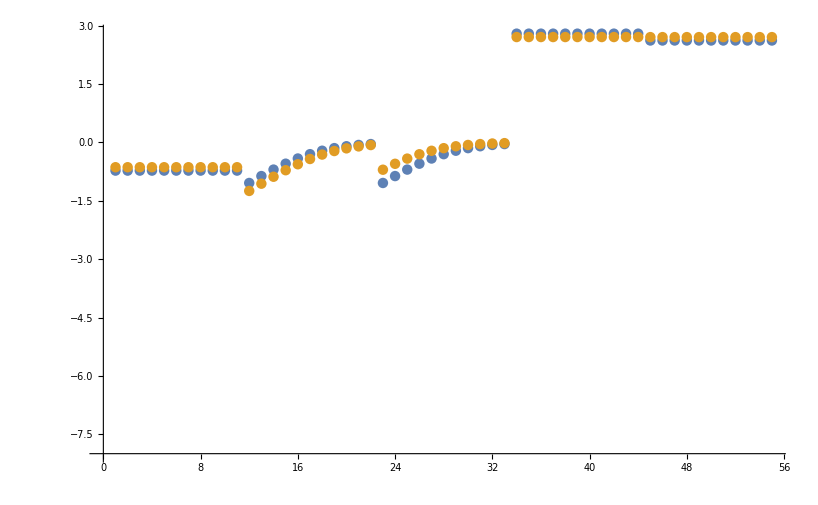

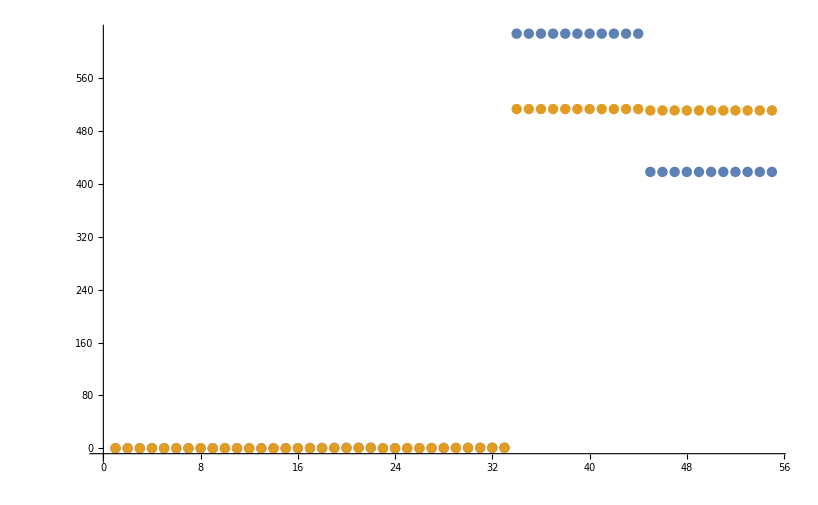

```mathematica
datasetI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

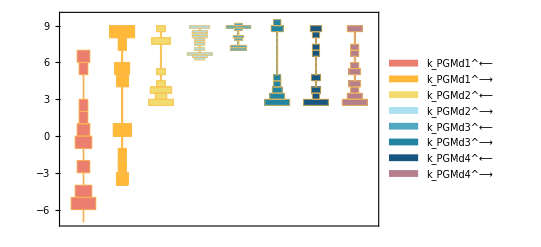

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

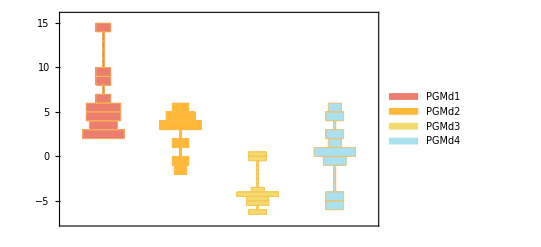

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24]
```

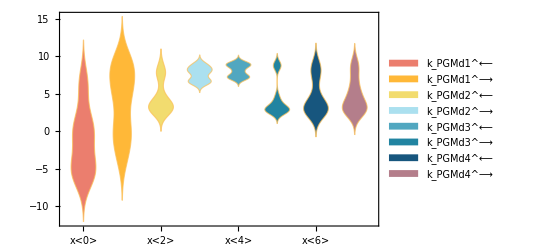

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)
(*Caution: If the distribution is narrow the smooth Kernel outputs an error*)
```

### Data Error Distribution

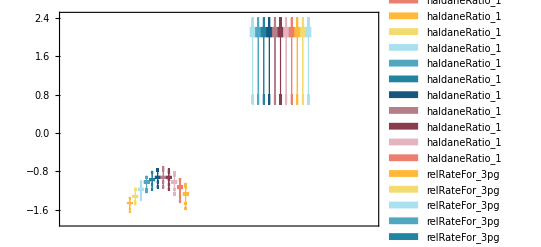

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];

fileNamesFormatted = StringReplace[fittingData[[All,-2]],"\\"->"/"];
inputPathFormatted = StringReplace[inputPath,"\\"->"/"];
funcNames=
Table[
	StringCases[func,RegularExpression[StringJoin[{inputPathFormatted,"/", "(.*).txt"}]]->"$1"][[1]],{func,fileNamesFormatted}];

DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Clustering (only recommended for >20 runs)

#### Specify which rate constant sets to use in clustering

```mathematica
(*Can cluster all solutions found or just the top N, if certain runs failed and the used would like to exclude their rate constants*)
bestNToCluster= Length[filteredDataList];
(*bestNToCluster = 20;*)
filteredDataListRed=filteredDataList[[1;;bestNToCluster]];
```

#### Cluster Parameters

```mathematica
(*clusters=FindClusters[Log10[filteredDataListRed[[All,2]]],Method->{"Agglomerate","Linkage"->"Complete","SignificanceTest"->{"Gap","Tolerance"->0.0001}}];(**)*)
clusters=FindClusters[Log10[filteredDataListRed[[All,2]]],Method->{"Optimize","Iterations"->2}];
medianParamCluster=Table[Median[clusters[[cluster,All,param]]],{cluster,Length[clusters]},{param,Length[clusters[[1,1]]]}](*Switch to log space and use mean?*);
clusterSqdRes=Table[(clusters[[cluster,paramSet,param]]-medianParamCluster[[cluster,param]])^2,{cluster,Length[clusters]},{paramSet,Length[clusters[[cluster]]]},{param,Length[clusters[[1,1]]]}];
clusterSSE=Table[Total[clusterSqdRes[[cluster,paramSet]]],{cluster,Length[clusterSqdRes]},{paramSet,Length[clusterSqdRes[[cluster]]]}];
bestClusterSSE=Table[SortBy[clusterSSE[[cluster]],Less],{cluster,Length[clusterSSE]}][[All,1]];
finalClusterParams={};
Table[If[clusterSSE[[cluster,paramSet]]==bestClusterSSE[[cluster]],finalClusterParams=Append[finalClusterParams,clusters[[cluster,paramSet]]]],{cluster,Length[clusterSSE]},{paramSet,Length[clusterSSE[[cluster]]]}];
```

#### Print Representative Parameter Sets for Each Cluster (Optional)

```mathematica
TableForm[finalClusterParams]
```

1.04894 | 5.21902 | 3.58435 | 6.76524 | 7.36026 | 2.78948 | 3.65396 | 4.40741
-4.89395 | -2.15338 | 3.75143 | 8.49348 | 9. | 3.58198 | 2.79948 | 2.83905

#### Parameter Cluster Plots (Optional)

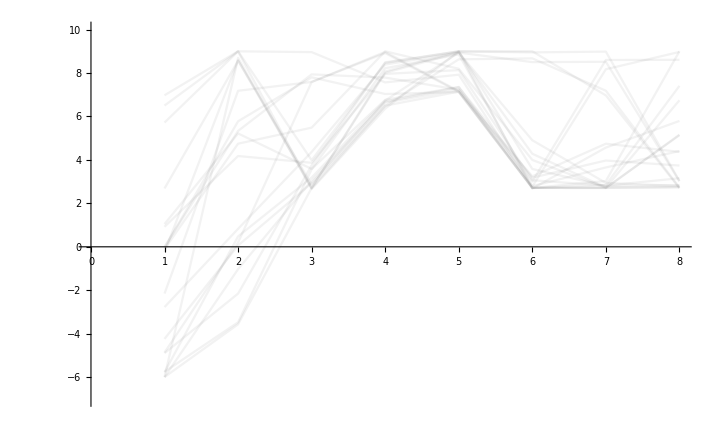

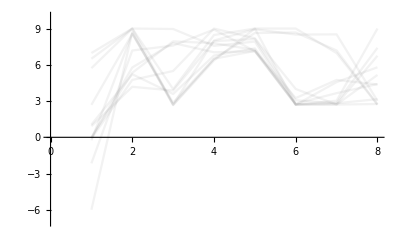
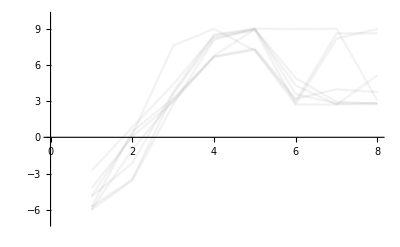

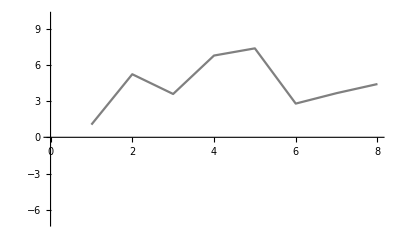
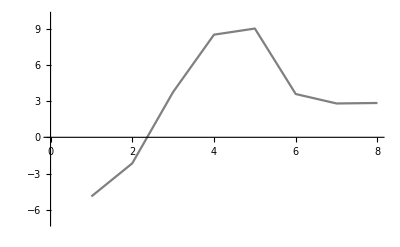

```mathematica
ListPlot[Log10[filteredDataListRed[[All,2]]],"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]](*All parameter sets*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]]&/@clusters
(*All parameter set clusters*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[1,Gray]]&/@finalClusterParams(*Representative parameter sets*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub,paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

data value | predicted value | error in %
0.0002 | 0.000331954 | 65.9768
0.00019 | 0.0000763769 | 59.8016

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
626.718 | 512.792 | 18.1782
417.812 | 510.642 | 22.2181

```mathematica
backCalculateRatios[haldaneRatiosList, KeqList[[All,3]],  paramFitSub]//TableForm
```

data value | predicted value | error in %
0.189 | 0.230992 | 22.218

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

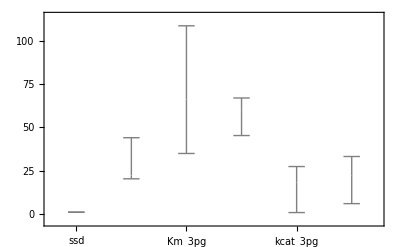

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

## Export data

```mathematica
(*Delete the directory if it already exists*)
dirExport= directoryMASSpyExport<>ToLowerCase[rxnName]<>"_MASSpyExport";
If[DirectoryQ[dirExport],
DeleteDirectory[dirExport]] ;
CreateDirectory[dirExport]
```

C:\MASSef\examples\Manuscript_Fitting\pgmd_MASSpyExport

```mathematica
(*Can take any number of solutions*)
indexLastGoodFit = 5;
```

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[dirExport<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

C:/MASSef/examples/Manuscript_Fitting/pgmd_MASSpyExport\rateconst_labels_pgmd.txt

```mathematica
Export[dirExport<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

C:/MASSef/examples/Manuscript_Fitting/pgmd_MASSpyExport\S_pgmd.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[dirExport<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_PGMd[c],E_PGMd[c]&23dpg,E_PGMd[c]&23dpg&2pg,23dpg[c],2pg[c],3pg[c],E_PGMd[c]&23dpg&3pg}

C:/MASSef/examples/Manuscript_Fitting/pgmd_MASSpyExport\species_pgmd.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[dirExport<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{PGMd1: 23dpg[c] + E_PGMd[c] <=> E_PGMd[c]&23dpg,PGMd2: 3pg[c] + E_PGMd[c]&23dpg <=> E_PGMd[c]&23dpg&3pg,PGMd3: E_PGMd[c]&23dpg&2pg <=> 2pg[c] + E_PGMd[c]&23dpg,PGMd4: E_PGMd[c]&23dpg&3pg <=> E_PGMd[c]&23dpg&2pg}

C:/MASSef/examples/Manuscript_Fitting/pgmd_MASSpyExport\reactions_pgmd.txt

```mathematica
solEnz = Import[directoryMASSpyExport <>mainFolder <>"/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[dirExport<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_PGMd[c],E_PGMd[c]&23dpg,E_PGMd[c]&23dpg&2pg,E_PGMd[c]&23dpg&3pg}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[dirExport<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

(k_PGMd1_rev*(k_PGMd2_rev*k_PGMd3_fwd*param_PGMd_total + k_PGMd3_fwd*k_PGMd4_fwd*param_PGMd_total + k_PGMd2_rev*k_PGMd4_rev*param_PGMd_total))/(23dpg(c)*3pg(c)*k_PGMd1_fwd*k_PGMd2_fwd*k_PGMd3_fwd + 23dpg(c)*k_PGMd1_fwd*k_PGMd2_rev*k_PGMd3_fwd + k_PGMd1_rev*k_PGMd2_rev*k_PGMd3_fwd + 23dpg(c)*2pg(c)*k_PGMd1_fwd*k_PGMd2_rev*k_PGMd3_rev + 23dpg(c)*3pg(c)*k_PGMd1_fwd*k_PGMd2_fwd*k_PGMd4_fwd + 23dpg(c)*k_PGMd1_fwd*k_PGMd3_fwd*k_PGMd4_fwd + k_PGMd1_rev*k_PGMd3_fwd*k_PGMd4_fwd + 23dpg(c)*2pg(c)*k_PGMd1_fwd*k_PGMd3_rev*k_PGMd4_fwd + 23dpg(c)*3pg(c)*k_PGMd1_fwd*k_PGMd2_fwd*k_PGMd4_rev + 23dpg(c)*k_PGMd1_fwd*k_PGMd2_rev*k_PGMd4_rev + k_PGMd1_rev*k_PGMd2_rev*k_PGMd4_rev + 23dpg(c)*2pg(c)*k_PGMd1_fwd*k_PGMd3_rev*k_PGMd4_rev)

```mathematica
(*Grab rate constant data from characteristic sets determined from clustering*)
Export[dirExport<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

C:/MASSef/examples/Manuscript_Fitting/pgmd_MASSpyExport\rateconst_clusters_pgmd.txt

```mathematica
solRateEq = Import[directoryMASSpyExport <>mainFolder <>"/input/absoluteFlux_"<>rxnName<>"_.m"];
```

```mathematica
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
```

```mathematica
Export[dirExport<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

C:/MASSef/examples/Manuscript_Fitting/pgmd_MASSpyExport\rateLaw_pgmd.txt